# Reissner-Nordström BH

```mathematica
(* Vorbereitungen fuer den Export *)
SetDirectory[NotebookDirectory[]];
cm=72/2.54;
```

```mathematica
ClearAll[EpiLabels]
EpiLabels[xpoint_,data_, labels_]:= 
With[{xpoints=If[Head@xpoint===List, xpoint, xpoint&/@ labels]}, (* erlaube Liste von xpoints *)
Text[
Rotate[labels⟦#⟧,ArcTan[ data'[xpoints⟦#⟧]⟦#⟧ ],{Left,Bottom}],
{xpoints⟦#⟧, 0 + data[xpoints⟦#⟧]⟦#⟧},
Background -> White
(* Opacity[0.8,White]*)
] & /@ Range@Length@data@1] (* 1: any value to introspect list*)
(* Colors of Penrose diagram: r+, r-, r=0, r*=Darker@Green *)
pointColors = RGBColor@@@ ({ {255,0,224}, {0,145,170},{204,0,0},{0,170,0}}/255);
```

## Plot der metrischen Funktion

```mathematica
(* Reissner Nordström *)
VRN[z_,ME_]=1-(2 ME z - 1)/z^2;
(* Bardeen *)
VBardeen[z_,ME_] = 1 - (2 ME z^2)/((1+z^2)^(3/2));
VHolo[z_,ME_] = 1 - (2 ME  z^2)/(z  (1+z^2));
VHself[z_,ME_] = 1 - With[{α= 3/Log[2] Log[3/2]}, (2 ME)/(z (1 + z^-α/2)^(3/α))]
```

1-(2 ME (1+1/2 z^(-(3 Log[3/2])/Log[2]))^(-Log[2]/Log[3/2]))/z

```mathematica
mes = {0,0.5,1,1.5};
rnGraphs[z_] = VRN[z,#]&/@ mes;
bardeenGraphs[z_] = VBardeen[z,#] & /@ mes;
rnLabels = "M/e="<>ToString@AccountingForm[#,1]&/@ mes
rnColors={Lighter@Blue, Darker@Yellow, Darker@Green, Red};
```

{M/e=0,M/e=0.5,M/e=1,M/e=2.}

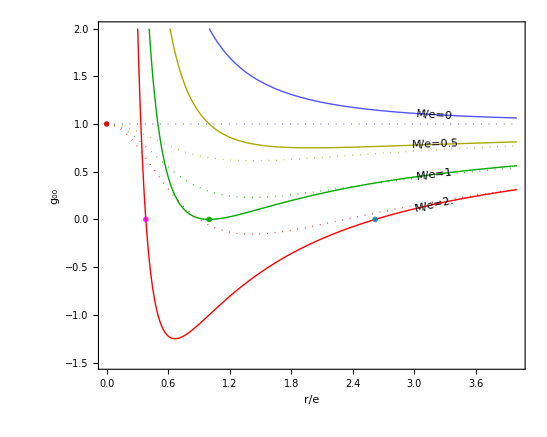

```mathematica
point[color_, xcoord_,ycoord_:0] := Inset[
Graphics@{Opacity[0.9], color, Disk[]},
(* {x,y}, {xOrig,yOrig}, scaling --> see Inset doku *)
{xcoord, ycoord}, {0,0}, 0.07
]
fig=Plot[
Evaluate@{rnGraphs@z,bardeenGraphs@z},
{z,0,4},
(*GridLines-> {{1},{1}},*)
PlotRange-> {-1.5,2},
PlotRangePadding->None,
PlotStyle->Join[rnColors,{Dotted,#}&/@rnColors],
Epilog-> {
EpiLabels[3.2, rnGraphs, rnLabels],
(* Gefunden mit First@FindRoot[rnGraphs[#][[4]]&[z],{z,2.5}] *)
point[pointColors⟦4⟧,1],
point[pointColors⟦3⟧,0,1],
point[pointColors⟦2⟧, 2.61803],
point[pointColors⟦1⟧, 0.38196],
},
Frame-> True,
FrameLabel-> {"r/e", "g_00"},
AspectRatio->0.8,
ImageSize-> 9cm
]
```

```mathematica
Export["../figures/reissner-nordstrom-me.pdf", Show@fig]
```

../figures/reissner-nordstrom-me.pdf